The mathematica code presented here for calculation of the demagnetising field for uniform polyhedra is taken from Fabbri [1]. This code is compared agains the calculation of Ravaud and Lemarquand [2].

```mathematica
Remove["Global`*"]
```

## Geometric Data (Overview)

Geometric data is supplied as a list of vertices, usually called VCL (Vertex Connectivity List) and a list of triple indices of trianges that constitute the surface of the geometry, usually called TIL (Triangle Index List). The TIL are indies in to the VCL array.

## Utility Geometry Functions

These functions are used to calculate basic properties of triangles found in geometric data. Centroid just calculates the centre of a cluster of points, and FaceNormal calculates the normal vector of a triangle face given a list of vertices and triangles.

```mathematica
(* Function to calculate the centroid of some points. *)
Centroid[points_]:=Module[{center},
center=Total[points]/Length[points]
]

(* Function to get the normal vector of a face. *)
FaceNormal[VCL_,TIL_,triangleIndex_]:=Module[{polyCenter,r1,r2,r3,l1,l2,n},
r1=VCL[[TIL[[triangleIndex,1]]]];
r2=VCL[[TIL[[triangleIndex,2]]]];
r3=VCL[[TIL[[triangleIndex,3]]]];
polyCenter=Centroid[VCL];
l1=r2-r1;
l2=r3-r1;
n=l1×l2;
Normalize[n]
]
```

## Utility Drawing Functions

These functions are used to disply geometries.

```mathematica
(* Function to draw the geometry (split in to triangles). *)
DrawPoly[VCL_,TIL_]:=Module[{triangleIndex,polygonGraphics,normalGraphics,n,nOffset},
polygonGraphics={};
normalGraphics={};
For[triangleIndex=1,triangleIndex≤Length[TIL],triangleIndex=triangleIndex+1,
AppendTo[polygonGraphics,Graphics3D[{Opacity[0.3],Polygon[{
VCL[[TIL[[triangleIndex,1]]]],
VCL[[TIL[[triangleIndex,2]]]],
VCL[[TIL[[triangleIndex,3]]]]}]}]];
n=FaceNormal[VCL,TIL,triangleIndex];
nOffset=Centroid[{
VCL[[TIL[[triangleIndex,1]]]],
VCL[[TIL[[triangleIndex,2]]]],
VCL[[TIL[[triangleIndex,3]]]]}];
AppendTo[normalGraphics,Graphics3D[{Red,Arrowheads[0.1],
Arrow[Tube[{nOffset,n+nOffset},0.05]]}]];
];
(*Show[polygonGraphics,normalGraphics]*)
Show[polygonGraphics]
]

(* Function to draw the geometry (split in to triangles) with surface normals illustrated. *)
DrawPolyNormals[VCL_,TIL_]:=Module[{triangleIndex,polygonGraphics,normalGraphics,n,nOffset,scaleFactor},
polygonGraphics={};
normalGraphics={};
scaleFactor=.01;
For[triangleIndex=1,triangleIndex≤Length[TIL],triangleIndex=triangleIndex+1,
AppendTo[polygonGraphics,Graphics3D[{Opacity[0.3],Polygon[{
VCL[[TIL[[triangleIndex,1]]]],
VCL[[TIL[[triangleIndex,2]]]],
VCL[[TIL[[triangleIndex,3]]]]}]}]];
n=FaceNormal[VCL,TIL,triangleIndex]*0.5*scaleFactor;
nOffset=Centroid[{
VCL[[TIL[[triangleIndex,1]]]],
VCL[[TIL[[triangleIndex,2]]]],
VCL[[TIL[[triangleIndex,3]]]]}];
AppendTo[normalGraphics,Graphics3D[{Red,Arrowheads[0.08],
Arrow[Tube[{nOffset,n+nOffset},0.03*scaleFactor]]}]];
];
Show[polygonGraphics,normalGraphics,Axes->True,AxesLabel->{x,y,z}]
]
```

## Geometric Data

This is The cube that will be uniformly magnetized.

```mathematica
VCL={
{-0.005,-0.005,-0.005},
{-0.005,-0.005,0.005},
{-0.005,0.005,-0.005},
{-0.005,0.005,0.005},
{0.005,-0.005,-0.005},
{0.005,-0.005,0.005},
{0.005,0.005,-0.005},
{0.005,0.005,0.005}};
TIL={{1,2,4},{1,4,3},{1,5,2},{2,5,6},{6,5,8},{5,7,8},{3,8,7},{3,4,8},{2,8,4},{2,6,8},{1,3,5},{3,7,5}};

(*
VCL={{0,0,0},{1,0,0},{0,1,0},{0,0,1}};
TIL={{1,2,3},{1,2,4},{1,4,3},{2,3,4}};

VCL={{1,1,1},{-1,-1,1},{-1,1,-1},{1,-1,-1}};
TIL={{1,3,2},{1,2,4},{1,4,3},{2,3,4}};

ELEM={1,2,3,4};
ELEM={1,3,4,2};
ELEM={1,4,2,3};
ELEM={2,1,4,3};
ELEM={2,3,1,4};
ELEM={2,4,3,1};
ELEM={3,1,2,4};
ELEM={3,2,4,1};
ELEM={3,4,1,2};
ELEM={4,1,3,2};
ELEM={4,2,1,3};
ELEM={4,3,2,1};
*)
(*ELEM={1,2,4,3};*)
(*ELEM={1,3,2,4};*)
(*ELEM={1,4,3,2};*)
(*ELEM={2,1,3,4};*)
(*ELEM={3,2,1,4};*)
(*ELEM={4,2,3,1};*)
(*ELEM={2,3,4,1};*)
(*ELEM={2,4,1,3};*)
(*ELEM={3,1,4,2};*)
(*ELEM={3,4,2,1};*)
(*ELEM={4,1,2,3};*)
(*ELEM={4,3,1,2};*)
	
(*
VCL={
{7.04973347,6.40004066,47.0401251},
{8.42138536,7.74863281,48.6727743},
{5.51920583,6.73141937,49.2364333},
{7.21300322,4.9866554,49.2250531}};

TIL={
{ELEM[[1]],ELEM[[3]],ELEM[[2]]},{ELEM[[1]],ELEM[[2]],ELEM[[4]]},{ELEM[[1]],ELEM[[4]],ELEM[[3]]},{ELEM[[2]],ELEM[[3]],ELEM[[4]]}
};
*)

DrawPolyNormals[VCL,TIL]
```

-Graphics3D-

## Vector Norm

Vector norm defined according to (19) in [1].

```mathematica
VNorm[r_]:=Module[{ϵ},
ϵ=0;
√(r[[1]]^2+r[[2]]^2+r[[3]]^2+ϵ^2)
]
```

## Solid Angle Function

Function to return a function that calculates the solid angle as seen by point r for a triangle defined by vertices r1, r2, r3.

```mathematica
SolidAngleFunction[VCL_,TIL_,triangleIndex_]:=Module[{r1,r2,r3},
r1=VCL[[TIL[[triangleIndex,1]]]];
r2=VCL[[TIL[[triangleIndex,2]]]];
r3=VCL[[TIL[[triangleIndex,3]]]];

(*
2ArcTan[(r1-{x,y,z}).((r2-{x,y,z})×(r3-{x,y,z})),(VNorm[r1-{x,y,z}]VNorm[r2-{x,y,z}]VNorm[r3-{x,y,z}]+VNorm[r3-{x,y,z}](r1-{x,y,z}).(r2-{x,y,z})+VNorm[r2-{x,y,z}](r1-{x,y,z}).(r3-{x,y,z})+VNorm[r1-{x,y,z}](r2-{x,y,z}).(r3-{x,y,z}))]
*)

2ArcTan[(VNorm[r1-{x,y,z}]VNorm[r2-{x,y,z}]VNorm[r3-{x,y,z}]+VNorm[r3-{x,y,z}](r1-{x,y,z}).(r2-{x,y,z})+VNorm[r2-{x,y,z}](r1-{x,y,z}).(r3-{x,y,z})+VNorm[r1-{x,y,z}](r2-{x,y,z}).(r3-{x,y,z})),(r1-{x,y,z}).((r2-{x,y,z})×(r3-{x,y,z}))]

]
```

## We Function

Function to return an expression that calculates We as seen by the point r for the edge defined by endpoints r1, r2.

```mathematica
WeFunction[r1_,r2_]:=Module[{},
Log[(VNorm[r2-{x,y,z}]+VNorm[r1-{x,y,z}]+VNorm[r2-r1])/(VNorm[r2-{x,y,z}]+VNorm[r1-{x,y,z}]-VNorm[r2-r1])]
]
```

## Wf Function

Function to return a function that calculates Wf (r) as seen by the point r defined for the triangle r1, r2, r3.

```mathematica
WfFunction[VCL_,TIL_,triangleIndex_]:=Module[{r1,r2,r3,nf,rf,Ω,u1,u2,u3,We1,We2,We3},
r1=VCL[[TIL[[triangleIndex,1]]]];
r2=VCL[[TIL[[triangleIndex,2]]]];
r3=VCL[[TIL[[triangleIndex,3]]]];

nf=FaceNormal[VCL,TIL,triangleIndex];
rf=Centroid[{r1,r2,r3}];
Ω=SolidAngleFunction[VCL,TIL,triangleIndex];

u1=Normalize[r2-r1];
u2=Normalize[r3-r2];
u3=Normalize[r1-r3];

We1=WeFunction[r1,r2];
We2=WeFunction[r2,r3];
We3=WeFunction[r3,r1];

(nf×(r1-{x,y,z}).u1)*We1+(nf×(r2-{x,y,z}).u2)*We2+(nf×(r3-{x,y,z}).u3)*We3-((rf-{x,y,z}).nf)*Ω
]
```

## Vector Potential

Function to return an expression that calculates the vector potential for a uniformly magnetized polyhedra defined by the triangles in VCL and TIL with magnetisation m.

```mathematica
MagneticVectorPotential[VCL_,TIL_,m_]:=Module[{r1,r2,r3,triangleIndex,A,cross,nf,Wf},
A=0;
For[triangleIndex=1,triangleIndex≤Length[TIL],triangleIndex=triangleIndex+1,
nf=FaceNormal[VCL,TIL,triangleIndex];
Wf=WfFunction[VCL,TIL,triangleIndex];

cross=m×nf;
A=A+{Wf*cross[[1]],Wf*cross[[2]],Wf*cross[[3]]}(**Wf[r];*);
];
A
]
```

## Holography

Function to return an expression that calculates the magnetic phase shift along beam direction n_d

```mathematica
MagneticPhaseShift[VCL_,TIL_,m_,nx_,ny_,nz_,px_,py_,pz_]:=Module[{r1,r2,r3,triangleIndex,A,cross,nf,Wf},
A=0;
For[triangleIndex=1,triangleIndex≤Length[TIL],triangleIndex=triangleIndex+1,
nf=FaceNormal[VCL,TIL,triangleIndex];
Wf=WfFunction[VCL,TIL,triangleIndex];

cross=m×nf;
A=A+{Wf*cross[[1]],Wf*cross[[2]],Wf*cross[[3]]}(**Wf[r];*);
];
Dot[{nx,ny,nz},(A/.{x->px+ζ nx,y->py+ζ ny,z->pz+ζ nz})]
]
```

## Scalar Potential

This is a calculation of the H field based on [2] (for more in - depth details see Revaud_and _Lemarquand.nb).

```mathematica
X[l_]:=Subscript[x,ToExpression[l]];
Y[l_]:=Subscript[y,ToExpression[l]];
Z[l_]:=Subscript[z,ToExpression[l]];

ξ[i_,j_,k_]:=√((x-X[i])^2+(y-Y[j])^2+(z-Z[k])^2);

Φ1[i_,j_,k_]:=Z[k]+(x-X[i])ArcTan[(z-Z[k])/(x-X[i])]+(y-Y[j])Log[z-Z[k]+ξ[i,j,k]]-(x-X[i])ArcTan[((y-Y[j])(z-Z[k]))/((x-X[i])ξ[i,j,k])]+(z-Z[k])Log[y-Y[j]+ξ[i,j,k]];
Φ2[i_,j_,k_]:=Z[k]+(y-Y[j])ArcTan[(z-Z[k])/(y-Y[j])]+(x-X[i])Log[z-Z[k]+ξ[i,j,k]]-(y-Y[j])ArcTan[((x-X[i])(z-Z[k]))/((y-Y[j])ξ[i,j,k])]+(z-Z[k])Log[x-X[i]+ξ[i,j,k]];
Φ3[i_,j_,k_]:=Y[j]+(z-Z[k])ArcTan[(y-Y[j])/(z-Z[k])]+(x-X[i])Log[y-Y[j]+ξ[i,j,k]]-(z-Z[k])ArcTan[((x-X[i])(y-Y[j]))/((z-Z[k])ξ[i,j,k])]+(y-Y[j])Log[x-X[i]+ξ[i,j,k]];

MagneticScalarPotential[J_,μ_,θ_,ϕ_,x1_,x2_,y1_,y2_,z1_,z2_]:=Module[{expr},
expr=J/(4π μ)*Sum[(-1)^(i+j+k)(Sin[ϕ]Cos[θ]Φ1[i,j,k]+Sin[ϕ]Sin[θ]Φ2[i,j,k]+Cos[ϕ]Φ3[i,j,k]),{i,1,2},{j,1,2},{k,1,2}]/.{Subscript[x, 1]->x1,Subscript[x, 2]->x2,Subscript[y, 1]->y1,Subscript[y, 2]->y2,Subscript[z, 1]->z1,Subscript[z, 2]->z2};
expr
]
```

## Example: Demagnetizing Field For a Uniformly Magnetized Cube, Vector Potential Vs. Scalar Potential

```mathematica
μ0=1;

(* Fabbri Method (via vector potential). *)
M=Normalize[{0,0,1}];
A=MagneticVectorPotential[VCL,TIL,M];
B=μ0/(4π) Curl[A,{x,y,z}];
HFab=Piecewise[{{B/μ0-M, 0≤x≤0.01∧0≤y≤0.01∧0≤z≤0.01}, {B, True}}];

(* Ravaud and Lemarquand Method (via scalar potential). *)
Φ=MagneticScalarPotential[1,μ0,0,0,0,0.01,0,0.01,0,0.01];
HRAndL={-D[Φ,x],-D[Φ,y],-D[Φ,z]};

(* Plots *)

MIN=-0.015;
MAX=0.015;

Show[VectorPlot3D[A/.{x->u,y->v,z->w},{u,MIN,MAX},{v,MIN,MAX},{w,MIN,MAX},VectorPoints->Fine,AxesLabel->{x,y,z},VectorStyle->"Arrow3D"],

DrawPoly[VCL,TIL]
]

(*
Show[VectorPlot3D[HFab/.{x->u,y->v,z->w},{u,MIN,MAX},{v,MIN,MAX},{w,MIN,MAX},VectorPoints->Fine,AxesLabel->{x,y,z},VectorStyle->"Arrow3D"],
DrawPoly[VCL,TIL]]

Show[VectorPlot3D[HRAndL/.{x->u,y->v,z->w},{u,MIN,MAX},{v,MIN,MAX},{w,MIN,MAX},VectorPoints->Fine,AxesLabel->{x,y,z},VectorStyle->"Arrow3D"],
DrawPoly[VCL,TIL]]

Print["Notice how at x=0 H is discontinuous and so Fabbri and Ravaud & Lemarquand give different answers near this point."];
Print[HFab/.{x->0,y->0.01/2,z->0.01/2}]
Print[HRAndL/.{x->0,y->0.01/2,z->0.01/2}]

Plot[{
(HFab/.{x->t,y->0.01/2,z->0.01/2})[[1]],
(HRAndL/.{x->t,y->0.01/2,z->0.01/2})[[1]]},{t,MIN,MAX},PlotRange->Full]
Plot[{
(HFab/.{x->t,y->0.01/2,z->0.01/2})[[2]],
(HRAndL/.{x->t,y->0.01/2,z->0.01/2})[[2]]},{t,MIN,MAX},PlotRange->Full]
Plot[{
(HFab/.{x->t,y->0.01/2,z->0.01/2})[[3]],
(HRAndL/.{x->t,y->0.01/2,z->0.01/2})[[3]]},{t,MIN,MAX},PlotRange->Full]
Plot[(HFab/.{x->t,y->0.01/2,z->0.01/2})[[3]],{t,MIN,MAX},PlotRange->Full]
*)
```

-Graphics3D-

## Effects of Changing ϵ in VNorm

As we change ϵ in VNorm, we find that we can get closer and closer to a point of discontinuity and have Fabbri and Ravaud & Lemarquand agree.

```mathematica
(*
Plot[HFab[[1]]/.{x->t,y->0.01/2,z->0.01/2},{t,MIN,MAX}]
Plot[HRAndL[[1]]/.{x->t,y->0.01/2,z->0.01/2},{t,MIN,MAX}]

Plot[HFab[[2]]/.{x->t,y->0.01/2,z->0.01/2},{t,MIN,MAX}]
Plot[HRAndL[[2]]/.{x->t,y->0.01/2,z->0.01/2},{t,MIN,MAX}]

Plot[HFab[[3]]/.{x->t,y->0.01/2,z->0.01/2},{t,MIN,MAX}]
Plot[HRAndL[[3]]/.{x->t,y->0.01/2,z->0.01/2},{t,MIN,MAX}]
*)

(HFab/.{x->0,y->0.01/2,z->0.01/2})[[2]]
(HRAndL/.{x->0,y->0.01/2,z->0.01/2})[[2]]

Print[HFab/.{x->0.0000000000001,y->0.01/2,z->0.01/2}]
Print[HRAndL/.{x->0.0000000000001,y->0.01/2,z->0.01/2}]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0.^2 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

ArcTan::indet: Indeterminate expression ArcTan[0.,0.] encountered.

Indeterminate

0.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0.^2 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

{2.42269×10^-12,Indeterminate,Indeterminate}

{-4.41744×10^-18,0.,-0.217953}

## Holography

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ζ near {ζ} = {2.17598×10^6}. NIntegrate obtained 0.019523 and 0.0198993 for the integral and error estimates.

0.019523

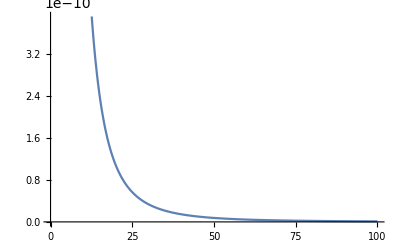

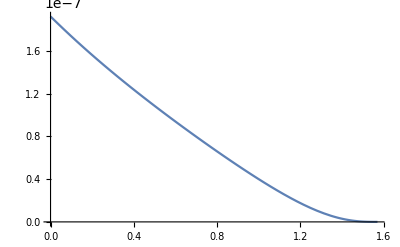

```mathematica
M=Normalize[{0,0,1}];
NN=10000;
ϕm=MagneticPhaseShift[VCL,TIL,M,0,1,0,1,1,1];
tϕm=ϕm/.ζ->Tan[ζ];

NIntegrate[ϕm,{ζ,0,∞}]

Plot[ϕm,{ζ,0,100}]
Plot[tϕm,{ζ,0,π/2}]
```

## Bibliography

[1] Fabbri, Massimo. Magnetic flux density and vector potential of uniform polyhedral sources. IEEE Transactions on Magnetics, 44.1 (2008) : 32 - 36.

[2] Romain Ravaud and Guy Lemarquand. Magnetic Field Produced by a Parallelepipedic Magnet of Various and Uniform Polarization. Progress In Electromagnetics Research, 98:207–219, 2009.

```mathematica
VCL={{1,0,-1/(√2)},{-1,0,-1/(√2)},{0,1,1/(√2)}};
TIL={{1,2,3}};
Ω=SolidAngleFunction[VCL,TIL,1];
N[2*π-6ArcSin[√(2/3)],20]
N[Ω/.{x->0,y->-1,z->1/(√2)},20]

we=WeFunction[{1,0,-1/(√2)},{-1,0,-1/(√2)}];
N[we/.{x->0,y->1,z->1/(√2)},20]
N[Log[3],20]

Wf=WfFunction[VCL,TIL,1];
N[-2 √6(-6ArcSin[√(2/3)]+2π)+√3+Log[3],20]
FullSimplify[Wf/.{x->0,y->-1,z->1/(√2)}]
N[FullSimplify[Wf/.{x->0,y->-1,z->1/(√2)}],20]
```

0.55128559843253080794

0.55128559843253080794

1.0986122886681096914

1.0986122886681096914

0.12992625882784638553

-4 √(2/3) ArcCot[5/(√2)]+√3 Log[3]

1.0026066893229783984